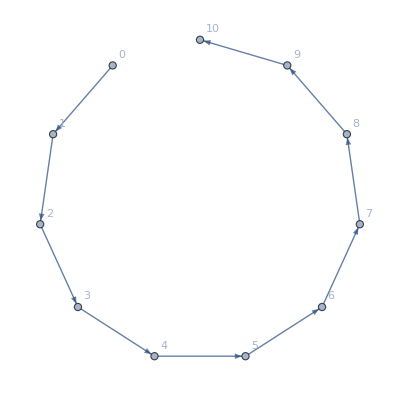

```mathematica
With[{
all=allGraphs5},
Graph[With[{list=Flatten[Table[Table[EdgeCount[all[k,"graph"]]->EdgeCount[all[child,"graph"]],{child,Flatten[Map[First,all[k,"children"]]]}],
{k,Keys[all]}]]},
DeleteDuplicates[list]]
,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
]
```

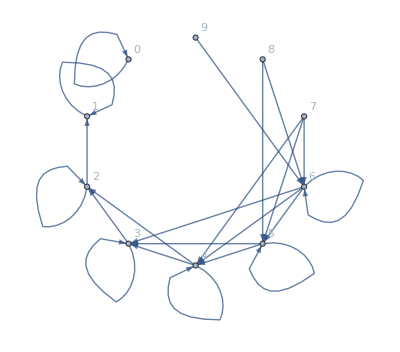

```mathematica
With[{
all=allGraphs5},
Graph[With[{list=Flatten[Table[Table[EdgeCount[all[k,"graph"]]->EdgeCount[all[child,"graph"]],{child,Flatten[Map[Last,all[k,"children"]]]}],
{k,Keys[all]}]]},
DeleteDuplicates[list]]
,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
]
```

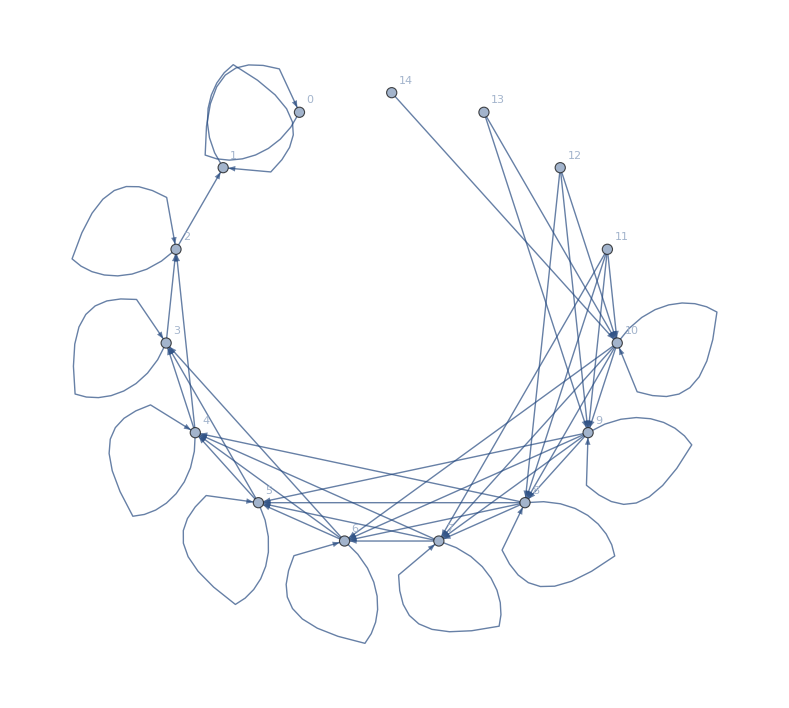

```mathematica
With[{
all=allGraphs6},
Graph[With[{list=Flatten[Table[Table[EdgeCount[all[k,"graph"]]->EdgeCount[all[child,"graph"]],{child,Flatten[Map[Last,all[k,"children"]]]}],
{k,Keys[all]}]]},
DeleteDuplicates[list]]
,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
]
```

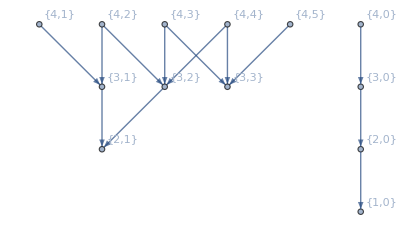

```mathematica
With[{
all=allGraphs4},
Graph[With[{list=Flatten[Table[Table[{VertexCount[all[k,"graph"]],EdgeCount[all[k,"graph"]]}->{VertexCount[all[child,"graph"]],EdgeCount[all[child,"graph"]]},{child,Flatten[Map[Last,all[k,"children"]]]}],
{k,Keys[all]}]]},
DeleteDuplicates[list]]
,VertexLabels->"Name", GraphLayout->"LayeredDigraphEmbedding"]
]
```

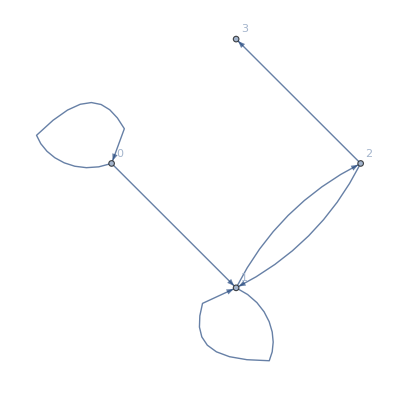

```mathematica
With[{
all=allGraphs3},
Graph[With[{list=Flatten[Table[Table[EdgeCount[all[k,"graph"]]->EdgeCount[all[child,"graph"]],{child,Flatten[all[k,"children"]]}],
{k,Keys[all]}]]},
DeleteDuplicates[list]]
,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
]
```

## Couples t

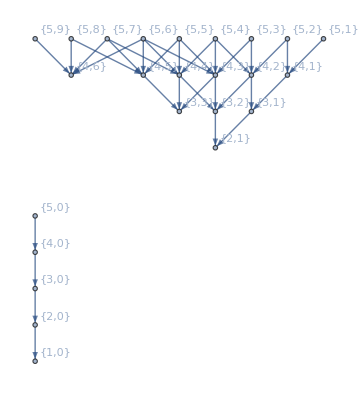

```mathematica
With[{
all=allGraphs5},
Graph[With[{list=Flatten[Table[Table[{VertexCount[all[k,"graph"]],EdgeCount[all[k,"graph"]]}->{VertexCount[all[child,"graph"]],EdgeCount[all[child,"graph"]]},{child,Flatten[Map[Last,all[k,"children"]]]}],
{k,Keys[all]}]]},
DeleteDuplicates[list]]
,VertexLabels->"Name", GraphLayout->"LayeredDigraphEmbedding"]
]
```

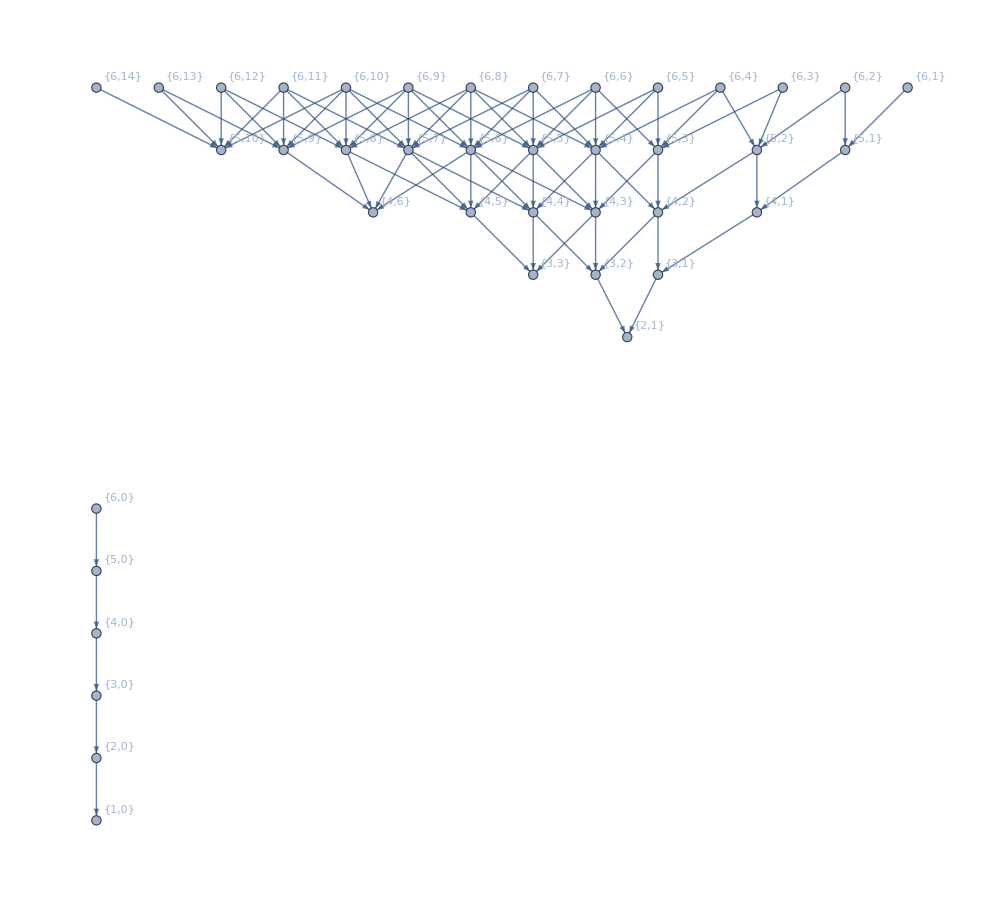

```mathematica
With[{
all=allGraphs6},
Graph[With[{list=Flatten[Table[Table[{VertexCount[all[k,"graph"]],EdgeCount[all[k,"graph"]]}->{VertexCount[all[child,"graph"]],EdgeCount[all[child,"graph"]]},{child,Flatten[Map[Last,all[k,"children"]]]}],
{k,Keys[all]}]]},
DeleteDuplicates[list]]
,VertexLabels->"Name", GraphLayout->"LayeredDigraphEmbedding"]
]
```

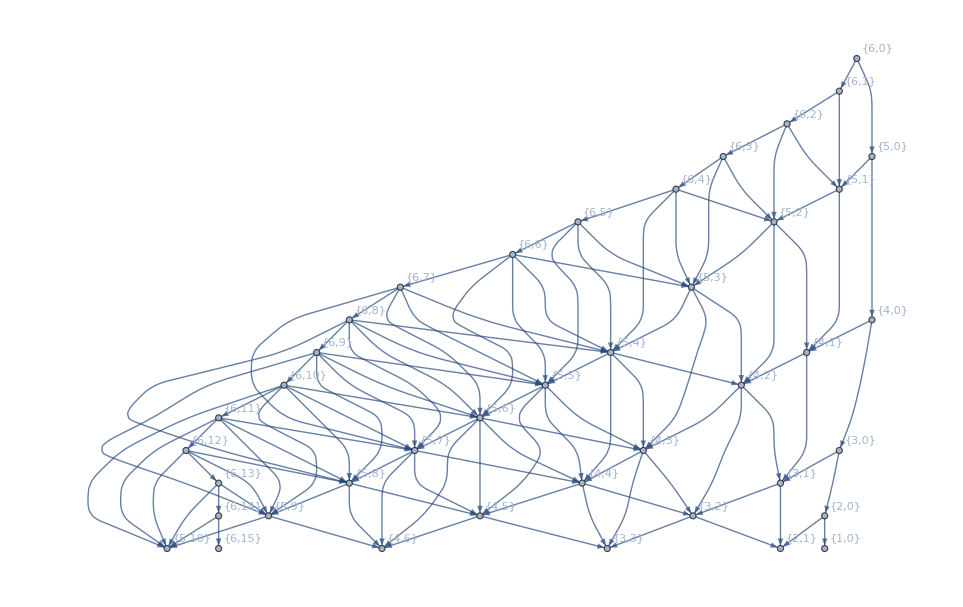

```mathematica
d6=With[{
all=allGraphs6},
Graph[With[{list=Flatten[Table[Table[{VertexCount[all[k,"graph"]],EdgeCount[all[k,"graph"]]}->{VertexCount[all[child,"graph"]],EdgeCount[all[child,"graph"]]},{child,Flatten[all[k,"children"]]}],
{k,Keys[all]}]]},
DeleteDuplicates[list]]
,VertexLabels->"Name", GraphLayout->"LayeredDigraphEmbedding"]
]
```

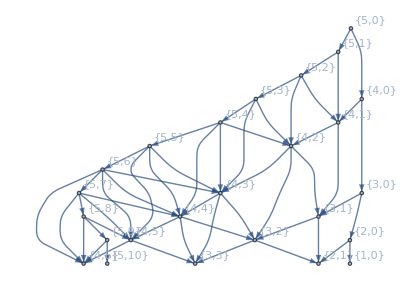

```mathematica
d5=With[{
all=allGraphs5},
Graph[With[{list=Flatten[Table[Table[{VertexCount[all[k,"graph"]],EdgeCount[all[k,"graph"]]}->{VertexCount[all[child,"graph"]],EdgeCount[all[child,"graph"]]},{child,Flatten[all[k,"children"]]}],
{k,Keys[all]}]]},
DeleteDuplicates[list]]
,VertexLabels->"Name", GraphLayout->"LayeredDigraphEmbedding"]
]
```

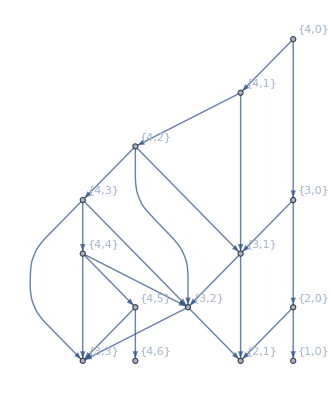

```mathematica
d4=With[{
all=allGraphs4},
Graph[With[{list=Flatten[Table[Table[{VertexCount[all[k,"graph"]],EdgeCount[all[k,"graph"]]}->{VertexCount[all[child,"graph"]],EdgeCount[all[child,"graph"]]},{child,Flatten[all[k,"children"]]}],
{k,Keys[all]}]]},
DeleteDuplicates[list]]
,VertexLabels->"Name", GraphLayout->"LayeredDigraphEmbedding"]
]
```

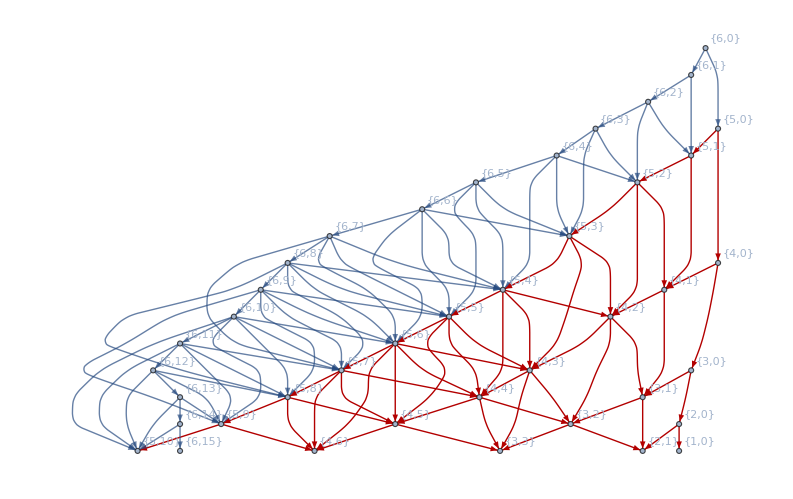

```mathematica
Graph[d6,GraphHighlight->EdgeList[d5]]
```

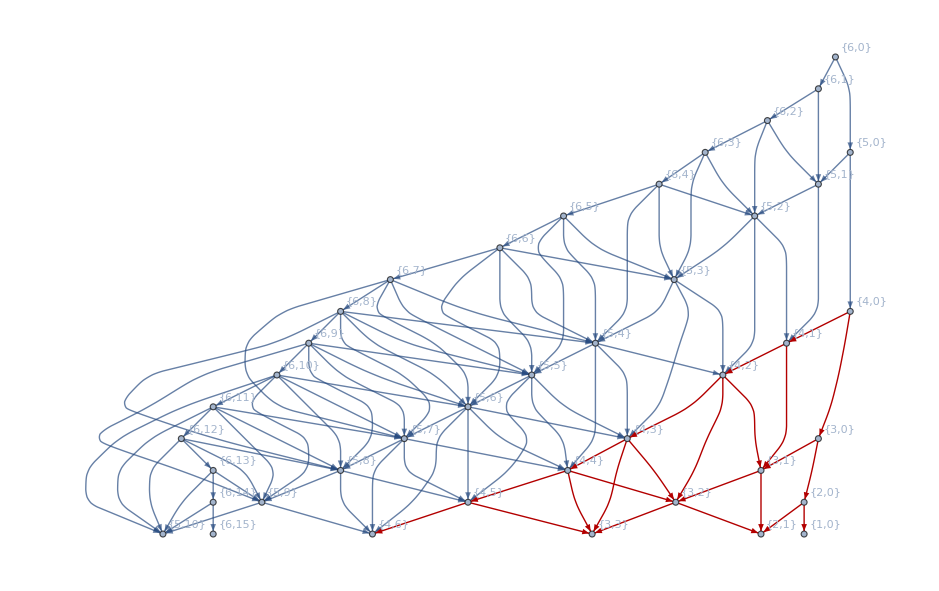

```mathematica
Graph[d6,GraphHighlight->EdgeList[d4], GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
Transitions[all_]:=Block[{edgecolors=Association[],vertexcolors=Association[], edge,edgecounts=Association[]},
Table[
Table[
vertexcolors[{VertexCount[all[k,"graph"]],EdgeCount[all[k,"graph"]]}]=ColourForKey[all,k];
(*vertexcolors[{VertexCount[all[childpair[[1]],"graph"]],EdgeCount[all[childpair[[1]],"graph"]]}]=ColourForKey[all,childpair[[1]]];*)
vertexcolors[{VertexCount[all[childpair[[2]],"graph"]],EdgeCount[all[childpair[[2]],"graph"]]}]=ColourForKey[all,childpair[[2]]];
(*edgecolors[{VertexCount[all[k,"graph"]],EdgeCount[all[k,"graph"]]}->{VertexCount[all[childpair[[1]],"graph"]],EdgeCount[all[childpair[[1]],"graph"]]}]={Thick,Blue};*)
edge={VertexCount[all[k,"graph"]],EdgeCount[all[k,"graph"]]}->{VertexCount[all[childpair[[2]],"graph"]],EdgeCount[all[childpair[[2]],"graph"]]};
If[KeyExistsQ[edgecounts,edge],edgecounts[edge]=edgecounts[edge]+1,edgecounts[edge]=1];
edgecolors[edge]=Red,
{childpair,all[k,"children"]}],

{k,Keys[all]}];
{Normal [edgecolors],Normal [vertexcolors],Normal [edgecounts]}
]
```

```mathematica
PlanarLabels[vertices_]:=Map[#->If[#[[1]]*3-6==#[[2]],Framed[ToString[#]],ToString[#]]&,vertices
]
```

```mathematica
PlanarEdgeLabels[edgecounts_]:=Map[#[[1]]->Tooltip["*",#[[2]]]&,edgecounts]
```

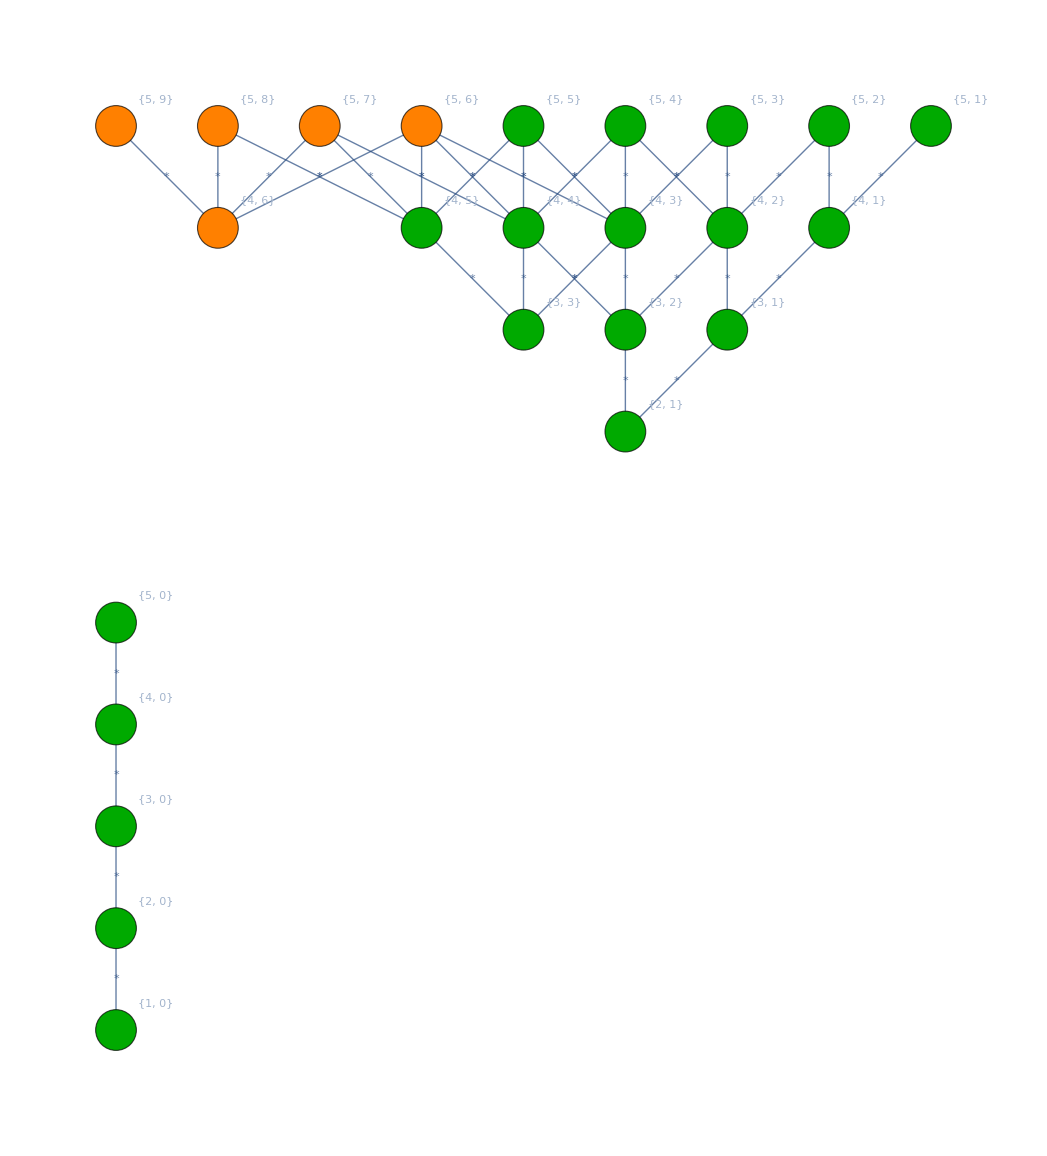

```mathematica
Block[{edgecolors,vertexcolors,edgecounts},
{edgecolors,vertexcolors,edgecounts}=Transitions[allGraphs5];
Graph[Map[First,edgecolors],EdgeLabels->PlanarEdgeLabels[edgecounts] ,VertexStyle->vertexcolors,VertexSize->Large, VertexLabels->PlanarLabels[Keys[vertexcolors]],GraphLayout->"LayeredDigraphEmbedding"]
]
```